# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../neuPackage/neutrino.wl"]
```

```mathematica
Get["../../neuPackage/neumat.wl"]
```

# Define Functions

Parameters

```mathematica
gF=1.17*10^(-11)(*MeV^(-2)*)
ye=0.5
```

1.17×10^-11

0.5

```mathematica
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
omegaV=deltamsquare13/(2 energy10)(*MeV*);(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093/2]
```

0.153077

```mathematica
fraction=10
lambdaN=fraction*Cos[2thetaV]omegaV
```

10

1.23955×10^-15

```mathematica
Cos[2thetaV]-(lambdaN/omegaV)^2
```

-89.9627

```mathematica
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];
init={psi1[0],psi2[0]}=={1,0};
endpointN=1600*15;
```

```mathematica
omegaM=omegaV √((lambdaN/omegaV-Cos[2thetaV])^2+Sin[2thetaV]^2)
```

1.11628×10^-15

Some test on the q values. In principle, we need to include q value up to 1. However, as I’ll show in the following, we actually need to include q value up to at least several hundred.

Lists

```mathematica
nNListTest={1,2,3,4,5,6}
nNListTestSym={n1,n2,n3,n4,n5,n6}
kNListTest={2.613874878374189273498126389572381489273897129879087581478947238946129836741984650871234,1.8,1.4,0.9,0.7,0.3}
kNListTestSym={k1,k2,k3,k4,k5,k6}
(*aNListTest=RandomReal[{0.000,0.200},6,WorkingPrecision->2]*lambdaN/OmegaMatter[thetamV,thetaV,omegaV]*)
aNListTest=0.1*kNListTest^(-5/3)
aNListTestSym={a1,a2,a3,a4,a5,a6}*lambdaN/OmegaMatter[thetamV,thetaV,omegaV]
phiNListTest={0,0,0,0,0,0}
```

{1,2,3,4,5,6}

{n1,n2,n3,n4,n5,n6}

{2.61387487837418927349812638957238148927389712987908758147894723894612983674198465087123,1.8,1.4,0.9,0.7,0.3}

{k1,k2,k3,k4,k5,k6}

{0.0201616,0.0375445,0.057076,0.119196,0.181205,0.743814}

{0.105988 a1,0.105988 a2,0.105988 a3,0.105988 a4,0.105988 a5,0.105988 a6}

{0,0,0,0,0,0}

Q Value

```mathematica
qValueOrderedList6=qValueOrderdList[listNGenerator[6,4],kNListTest,aNListTest,phiNListTest,thetamV]
```

{{{0,-3,1,3,2,3},0.},{{0,-3,1,4,2,0},0.},{{0,-2,0,3,1,4},0.},{{0,-2,0,3,4,-3},0.},{{0,-2,0,4,1,1},0.},531431,{{0,2,-1,-3,2,-3},ComplexInfinity},{{0,2,0,-4,0,0},ComplexInfinity},{{0,2,0,-3,0,-3},ComplexInfinity},{{0,2,1,-4,-2,0},ComplexInfinity},{{0,2,1,-3,-2,-3},ComplexInfinity}}
 |  |  |  |

```mathematica
(*Export["export/qValueOrderedList6-4.dat",qValueOrderedList6]*)
```

```mathematica
qValueOrderedList6=Import["export/qValueOrderedList6-4.dat","TSV"]
```

{{{0, -3, 1, 3, 2, 3},0.},{{0, -3, 1, 4, 2, 0},0.},{{0, -2, 0, 3, 1, 4},0.},{{0, -2, 0, 3, 4, -3},0.},{{0, -2, 0, 4, 1, 1},0.},{{0, -2, 1, 3, -1, 4},0.},{{0, -2, 1, 3, 2, -3},0.},531427,{{0, 2, -1, -4, 2, 0},ComplexInfinity},{{0, 2, -1, -3, -1, 4},ComplexInfinity},{{0, 2, -1, -3, 2, -3},ComplexInfinity},{{0, 2, 0, -4, 0, 0},ComplexInfinity},{{0, 2, 0, -3, 0, -3},ComplexInfinity},{{0, 2, 1, -4, -2, 0},ComplexInfinity},{{0, 2, 1, -3, -2, -3},ComplexInfinity}}
 |  |  |  |

```mathematica
Part[qValueOrderedList6,1;;300]//Grid
```

{0, -3, 1, 3, 2, 3} | 0.
{0, -3, 1, 4, 2, 0} | 0.
{0, -2, 0, 3, 1, 4} | 0.
{0, -2, 0, 3, 4, -3} | 0.
{0, -2, 0, 4, 1, 1} | 0.
{0, -2, 1, 3, -1, 4} | 0.
{0, -2, 1, 3, 2, -3} | 0.
{0, -2, 1, 4, -1, 1} | 0.
{0, -2, 2, 3, 0, -3} | 0.
{0, -2, 4, 2, -4, 0} | 0.
{0, -1, 0, 1, 4, -3} | 0.
{0, -1, 0, 2, 1, 1} | 0.
{0, -1, 0, 3, 1, -2} | 0.
{0, -1, 0, 4, -2, 2} | 0.
{0, -1, 1, 1, 2, -3} | 0.
{0, -1, 1, 2, -1, 1} | 0.
{0, -1, 2, 1, 0, -3} | 0.
{0, -1, 4, -1, -4, 3} | 0.
{0, -1, 4, 0, -4, 0} | 0.
{0, 0, -4, 4, 3, 3} | 0.
{0, 0, -2, 2, 2, 2} | 0.
{0, 0, -1, 2, 0, 2} | 0.
{0, 0, 0, -1, 4, -3} | 0.
{0, 0, 0, 0, 1, 1} | 0.
{0, 0, 0, 1, 1, -2} | 0.
{0, 0, 0, 2, -2, 2} | 0.
{0, 0, 1, -1, 2, -3} | 0.
{0, 0, 1, 0, -1, 1} | 0.
{0, 0, 2, -1, 0, -3} | 0.
{0, 0, 2, 1, -3, -2} | 0.
{0, 0, 4, -2, -4, 0} | 0.
{0, 1, -4, 3, 3, 0} | 0.
{0, 1, -4, 4, 3, -3} | 0.
{0, 1, -2, 0, 2, 2} | 0.
{0, 1, -1, 0, 0, 2} | 0.
{0, 1, 0, -2, 1, 1} | 0.
{0, 1, 0, -1, 1, -2} | 0.
{0, 1, 0, 0, -2, 2} | 0.
{0, 1, 1, -4, 2, 0} | 0.
{0, 1, 1, -3, -1, 4} | 0.
{0, 1, 1, -3, 2, -3} | 0.
{0, 1, 2, -1, -3, -2} | 0.
{0, 2, -4, 0, 3, 3} | 0.
{0, 2, -4, 1, 3, 0} | 0.
{0, 2, -2, -2, 2, 2} | 0.
{0, 2, -1, -2, 0, 2} | 0.
{0, 2, 0, -4, 1, 1} | 0.
{0, 2, 0, -2, -2, 2} | 0.
{0, 2, 1, -4, -1, 1} | 0.
{0, 4, -4, -4, 3, 3} | 0.
{0, 4, -4, -3, 3, 0} | 0.
{0, 0, 0, -1, 1, 4} | 1.08959×10^-10
{0, 0, 1, 1, -1, -2} | 8.65502×10^-10
{0, 0, 1, -1, -1, 4} | 5.34415×10^-9
{0, -1, 0, 1, 1, 4} | 1.04471×10^-8
{0, 1, -1, 1, 0, -1} | 1.91181×10^-8
{0, 0, -1, 0, 3, 1} | 3.61573×10^-8
{0, 1, 0, 1, -2, -1} | 4.60149×10^-8
{0, 0, -1, 3, 0, -1} | 2.72526×10^-7
{0, 1, 1, -1, -1, -2} | 3.31943×10^-7
{0, -1, 1, 1, -1, 4} | 5.12406×10^-7
{0, 0, 0, 3, -2, -1} | 6.55939×10^-7
{0, 0, -1, 1, 3, -2} | 9.26059×10^-7
{0, -1, 2, 0, 0, 0} | 1.64158×10^-6
{0, 2, -1, 0, 0, -4} | 1.70243×10^-6
{0, -1, 1, 0, 2, 0} | 1.97528×10^-6
{0, 0, 2, 0, -3, 1} | 3.54735×10^-6
{0, 2, -1, -1, 0, -1} | 3.66628×10^-6
{0, 0, -1, -1, 3, 4} | 3.81204×10^-6
{0, 1, -1, 2, 0, -4} | 4.03712×10^-6
{0, 2, 0, 0, -2, -4} | 4.09755×10^-6
{0, 1, 1, -2, -1, 1} | 4.42045×10^-6
{0, -1, 2, -1, 0, 3} | 6.63983×10^-6
{0, 0, 2, -2, 0, 0} | 7.78594×10^-6
{0, 2, 0, -1, -2, -1} | 8.8243×10^-6
{0, 0, 1, -2, 2, 0} | 9.36862×10^-6
{0, 1, 0, 2, -2, -4} | 9.71687×10^-6
{0, -1, 1, -1, 2, 3} | 0.0000106527
{0, 1, 0, -3, 1, 4} | 0.0000285579
{0, -1, 0, 0, 4, 0} | 0.0000287834
{0, 1, -1, -1, 3, -2} | 0.0000887921
{0, -1, 1, 3, -1, -2} | 0.000113424
{0, 0, -1, 4, 0, -4} | 0.000115156
{0, 0, 2, -3, 0, 3} | 0.0001262
{0, 0, 0, -2, 4, 0} | 0.000136518
{0, 0, 1, -3, 2, 3} | 0.000151853
{0, -1, 0, -1, 4, 3} | 0.000155229
{0, 1, -2, 1, 2, -1} | 0.000221423
{0, 1, 1, 0, -4, 2} | 0.000242611
{0, 0, 0, 4, -2, -4} | 0.000277168
{0, 0, 2, -1, -3, 4} | 0.000373994
{0, 2, -2, 0, -1, 3} | 0.000431604
{0, 2, 0, -3, 1, -2} | 0.000443474
{0, -1, -1, 4, 0, 2} | 0.000894095
{0, 1, -2, 2, -1, 3} | 0.0010235
{0, -1, -1, 1, 3, 4} | 0.00109651
{0, 0, 1, 2, -4, 2} | 0.00115069
{0, -2, 2, 1, 0, 3} | 0.00127332
{0, 1, -1, -2, 3, 1} | 0.00157658
{0, 0, 3, -1, -2, -3} | 0.00160415
{0, -2, 1, 1, 2, 3} | 0.00204287
{0, 0, 0, -3, 4, 3} | 0.00221278
{0, 2, -1, 0, -3, 3} | 0.00313803
{0, -1, -1, 2, 3, 1} | 0.00315315
{0, 0, -2, 3, 2, -1} | 0.00315637
{0, 1, 1, 1, -4, -1} | 0.00483914
{0, 1, -1, 2, -3, 3} | 0.00744148
{0, 1, 2, -3, 0, -3} | 0.0121003
{0, 2, -2, 0, 2, -4} | 0.0197173
{0, 2, 1, -3, -1, -2} | 0.0217513
{0, 0, 1, 3, -4, -1} | 0.0229938
{0, 0, -2, 4, -1, 3} | 0.0291947
{0, -2, 0, 1, 4, 3} | 0.0297684
{0, -1, 2, 1, -3, 4} | 0.0358592
{0, 2, -2, 1, -1, 0} | 0.0363413
{0, 2, -2, -1, 2, -1} | 0.0424624
{0, -1, 3, -1, 1, -4} | 0.0443901
{0, 1, -2, 2, 2, -4} | 0.0467574
{0, -1, 3, 0, -2, 0} | 0.0570398
{0, 1, 0, -3, 4, -3} | 0.106083
{0, -1, 2, -1, 3, -4} | 0.107577
{0, -2, 3, 0, 1, -1} | 0.107658
{0, -1, -1, 3, 3, -2} | 0.12136
{0, -2, 2, 2, 0, 0} | 0.143162
{0, 2, 1, 0, -4, -4} | 0.143639
{0, -1, 3, -1, -2, 3} | 0.153809
{0, -1, 3, 1, -2, -3} | 0.153809
{0, -1, 2, 2, -3, 1} | 0.154676
{0, 1, 2, -2, -3, 1} | 0.154676
{0, -2, 1, 2, 2, 0} | 0.172263
{0, 2, -3, 0, 1, 3} | 0.190555
{0, -1, 3, -2, 1, -1} | 0.191473
{0, -2, 2, 0, 3, -1} | 0.195678
{0, 0, -1, 4, -3, 3} | 0.212264
{0, 3, -1, -2, 0, -4} | 0.222705
{0, 2, -1, 1, -3, 0} | 0.264224
{0, 0, 3, -2, -2, 0} | 0.270537
{0, 1, -3, 2, 1, 3} | 0.301253
{0, 2, 1, -1, -4, -1} | 0.309334
{0, 1, 1, 2, -4, -4} | 0.340623
{0, 3, -2, 0, -1, -3} | 0.372463
{0, -1, 2, -2, 3, -1} | 0.464027
{0, 1, -1, -3, 3, 4} | 0.499566
{0, 1, -2, 3, -1, 0} | 0.518022
{0, 2, -2, 2, -1, -3} | 0.58883
{0, 0, 3, -3, 1, -4} | 0.632776
{0, 3, -1, 0, -3, -3} | 0.90268
{0, 0, -2, 4, 2, -4} | 1.33373
{0, 2, -1, 2, -3, -3} | 1.42705
{0, 3, -1, -3, 0, -1} | 1.44146
{0, 0, 2, -3, 3, -4} | 1.53351
{0, 3, 0, -2, -2, -4} | 1.60807
{0, -2, 3, -1, 1, 2} | 1.83821
{0, -2, 0, 2, 4, 0} | 2.51019
{0, -2, 2, -1, 3, 2} | 2.78427
{0, -1, 4, -1, -1, -4} | 2.90351
{0, 3, 0, -3, -2, -1} | 3.46942
{0, 1, -3, 0, 4, 2} | 3.50293
{0, 1, -1, 3, -3, 0} | 3.76635
{0, 1, 2, -4, 0, 0} | 4.08346
{0, 0, 3, -3, -2, 3} | 4.38505
{0, 0, 3, -4, 1, -1} | 7.28221
{0, 1, -2, 4, -1, -3} | 8.39771
{0, -2, 3, 1, 1, -4} | 8.51269
{0, 0, 1, 4, -4, -4} | 9.71608
{0, -2, 4, 0, -1, -1} | 10.5626
{0, -1, 3, -3, 1, 2} | 11.4636
{0, -1, 4, -2, -1, -1} | 12.524
{0, 0, -3, 4, 1, 3} | 12.8896
{0, 0, 2, -4, 3, -1} | 13.2361
{0, -1, 2, 3, -3, -2} | 15.8752
{0, 0, -3, 2, 4, 2} | 16.6142
{0, 1, -1, 4, -3, -3} | 20.3522
{0, -2, 2, 1, 3, -4} | 20.6302
{0, 2, 1, -2, -4, 2} | 21.158
{0, 2, -3, 1, 1, 0} | 21.3931
{0, 2, -1, -3, 3, -2} | 23.2731
{0, 1, -3, 1, 4, -1} | 23.2899
{0, -1, 2, -3, 3, 2} | 27.7816
{0, 3, -2, -1, -1, 0} | 31.3616
{0, 1, 0, -4, 4, 0} | 35.7995
{0, -1, -2, 4, 2, 2} | 41.4212
{0, 1, 2, -3, -3, 4} | 49.0117
{0, 3, -1, -4, 0, 2} | 49.3221
{0, -2, 3, 1, -2, 3} | 58.9918
{0, 3, -1, -1, -3, 0} | 76.0061
{0, 3, -3, 0, 1, -3} | 91.3577
{0, -2, -1, 3, 3, 4} | 95.8019
{0, 3, -2, -2, -1, 3} | 112.921
{0, 1, -3, 3, 1, 0} | 114.354
{0, 2, -3, 2, 1, -3} | 115.543
{0, 0, 4, -3, -1, -4} | 124.168
{0, -2, 4, -1, -1, 2} | 135.265
{0, 0, 4, -1, -4, -3} | 224.975
{0, -1, 1, 4, -4, 2} | 301.749
{0, 0, 0, 0, 0, 3} | 318.614
{0, 3, -1, -2, -3, 3} | 410.504
{0, 1, 3, -3, -2, -3} | 420.446
{0, 3, 0, -4, -2, 2} | 474.85
{0, -3, 3, 1, 1, 2} | 660.97
{0, -3, 2, 3, 0, 3} | 667.502
{0, 0, 4, -4, -1, -1} | 714.482
{0, -2, -1, 4, 3, 1} | 826.892
{0, 2, -1, -4, 3, 1} | 826.892
{0, 0, 0, 0, 0, 2} | 917.897
{0, -1, 4, -3, -1, 2} | 964.059
{0, 0, -3, 3, 4, -1} | 995.985
{0, 1, -3, 4, 1, -3} | 1235.87
{0, 0, 0, 0, 0, 4} | 1416.92
{0, -3, 2, 1, 3, 2} | 1441.65
{0, -2, 4, 1, -1, -4} | 1670.42
{0, 0, 0, 0, 1, 2} | 2434.22
{0, 3, -2, -2, 2, -4} | 2579.34
{0, 0, 0, 0, 0, 1} | 2835.11
{0, 2, 2, -3, -3, -2} | 3044.39
{0, 0, 0, 1, 0, 1} | 3051.41
{0, 0, 0, 0, 0, -2} | 3671.59
{0, 3, -4, 0, 0, 4} | 4162.42
{0, 3, -3, 0, -2, 4} | 4173.57
{0, 2, -4, 2, 0, 4} | 4386.94
{0, 1, -3, 2, 4, -4} | 4918.07
{0, -2, 3, 2, -2, 0} | 4974.42
{0, 0, 0, 0, 0, -1} | 5265.2
{0, 2, -3, 2, -2, 4} | 5278.43
{0, 0, 1, 0, 0, -1} | 5417.73
{0, 0, 0, 0, 0, -3} | 6053.66
{0, 3, -3, -1, 1, 0} | 6153.89
{0, 2, -3, 0, 4, -4} | 6221.77
{0, 0, 0, 1, 0, 2} | 6915.49
{0, 0, 0, 0, 1, 3} | 8238.26
{0, 3, -4, 1, 0, 1} | 8964.
{0, 3, -3, 1, -2, 1} | 8988.02
{0, -2, 2, 3, -3, 4} | 9398.99
{0, 1, -4, 2, 3, 3} | 10541.6
{0, -3, 0, 3, 4, 3} | 11703.9
{0, 3, -2, 0, -4, 4} | 12161.2
{0, 0, 0, 1, 0, -1} | 12205.6
{0, 0, 0, 0, 2, -1} | 13039.8
{0, 2, -3, -1, 4, -1} | 13398.9
{0, 0, 0, 0, 1, -1} | 13963.1
{0, 0, 0, 0, 0, -4} | 15586.1
{0, 3, -2, -3, 2, -1} | 16694.8
{0, 0, 1, 0, 0, -2} | 16882.7
{0, -3, 3, 2, 1, -1} | 17604.1
{0, 0, 0, 0, -1, -1} | 18617.4
{0, 0, 0, 0, -1, -2} | 18662.4
{0, 0, 0, 1, 0, 3} | 19203.6
{0, 2, -2, 2, -4, 4} | 19225.8
{0, -1, 4, 1, -4, -3} | 21571.
{0, 1, 0, 0, 0, -2} | 22002.4
{0, 0, 1, 0, 0, 1} | 24539.1
{0, 3, -2, 1, -4, 1} | 26189.8
{0, 0, 0, 1, 0, 0} | 26827.4
{0, 0, 0, 1, -1, 3} | 30093.3
{0, 1, 0, 0, 0, -3} | 30549.2
{0, 0, 0, 0, 1, 4} | 30851.9
{0, 1, -4, 4, 0, 4} | 31282.6
{0, 0, 0, 1, 1, -1} | 32368.8
{0, 0, 0, 0, -1, 1} | 32580.5
{0, 3, -3, -2, 1, 3} | 33236.7
{0, 0, 0, -1, 0, -1} | 33565.5
{0, 0, 1, 0, 0, 2} | 33765.4
{0, -3, 2, 2, 3, -1} | 34130.3
{0, 0, 0, -1, 0, -2} | 34577.4
{0, 0, 0, 0, -1, -3} | 35699.1
{0, 1, 0, 0, 0, -1} | 38833.6
{0, 0, 0, 1, -1, 2} | 39735.7
{0, -2, 3, 3, -2, -3} | 40314.5
{0, 0, 0, 0, 2, -2} | 40634.7
{0, 2, -4, 3, 0, 1} | 42591.7
{0, 2, -3, 3, -2, 1} | 42705.8
{0, 0, 0, 1, 0, -2} | 48408.4
{0, 0, 0, -1, 0, 1} | 48822.5
{0, 0, 0, 0, 1, 0} | 52611.9
{0, 1, -3, 4, -2, 4} | 56459.5
{0, 0, 0, 0, 2, 1} | 59062.8
{0, 1, 0, 0, 0, 1} | 61024.2
{0, 4, -2, -2, -1, -3} | 64965.5
{0, 0, 0, 0, -1, 4} | 65131.8
{0, 0, 0, 1, 1, 1} | 66441.2
{0, 0, 0, 1, 0, 4} | 67100.8
{0, 0, 0, -1, 0, -3} | 67212.7
{0, 1, 0, 0, 0, 2} | 77008.3
{1, 0, 0, 0, -1, -3} | 77953.9
{0, 0, 1, 0, 0, 3} | 79495.
{0, -2, 2, 4, -3, 1} | 81125.2
{0, 0, 0, 0, 2, 2} | 81269.4
{0, 0, 0, 1, 1, 2} | 86696.1
{0, 0, 0, 0, -1, 3} | 87874.8
{0, 0, 0, -1, 0, 2} | 89901.3
{0, -3, 4, 1, -1, 2} | 90790.
{0, 0, 1, -1, 0, 2} | 92505.6
{0, -3, 4, 0, 2, -2} | 92844.1
{0, 3, 1, -2, -4, -4} | 93951.1
{0, 0, -1, 0, 0, -1} | 94650.9
{0, 0, 0, 0, 1, -2} | 94934.7
{0, 0, 0, 0, -1, -4} | 99411.6
{0, 0, -1, 0, 0, -2} | 101296.
{0, 0, 0, 2, 0, -2} | 104356.
{0, -2, 4, -2, 2, -2} | 104841.

To Wavelength

```mathematica
?"neumat`*"
```

```mathematica
?widthNList
```

"Calculate the width; Example, widthNList[list of n's,list of k's,list of a's,list of ϕ's,thetam] and here lists are in the form {0.999,0.6,0.4}. Output is in unit of ω_m ."

```mathematica
widthNList[ToExpression[First@qValueOrderedList6[[2]]],kNListTest,aNListTest,phiNListTest,thetamV]
```

1.6384×10^-21

```mathematica
Grid[
Table[
{ToExpression@First@qValueOrderedList6[[col]],widthNList[ToExpression@First@qValueOrderedList6[[col]],kNListTest,aNListTest,phiNListTest,thetamV]},
{col,1,300(*Length[qValueOrderedList6]*)}],
Frame->All]
```

{0,-3,1,3,2,3} | 5.52908×10^-19
{0,-3,1,4,2,0} | 1.6384×10^-21
{0,-2,0,3,1,4} | 4.05445×10^-14
{0,-2,0,3,4,-3} | 1.09148×10^-17
{0,-2,0,4,1,1} | 4.6974×10^-15
{0,-2,1,3,-1,4} | 8.26638×10^-16
{0,-2,1,3,2,-3} | 1.59048×10^-16
{0,-2,1,4,-1,1} | 9.57725×10^-17
{0,-2,2,3,0,-3} | 1.91379×10^-16
{0,-2,4,2,-4,0} | 6.36558×10^-25
{0,-1,0,1,4,-3} | 2.86086×10^-12
{0,-1,0,2,1,1} | 2.46372×10^-9
{0,-1,0,3,1,-2} | 4.80091×10^-11
{0,-1,0,4,-2,2} | 5.15908×10^-14
{0,-1,1,1,2,-3} | 4.16879×10^-11
{0,-1,1,2,-1,1} | 5.02313×10^-11
{0,-1,2,1,0,-3} | 5.0162×10^-11
{0,-1,4,-1,-4,3} | 2.05874×10^-20
{0,-1,4,0,-4,0} | 5.5514×10^-20
{0,0,-4,4,3,3} | 7.3844×10^-22
{0,0,-2,2,2,2} | 2.81148×10^-12
{0,0,-1,2,0,2} | 3.25622×10^-8
{0,0,0,-1,4,-3} | 2.74304×10^-10
{0,0,0,0,1,1} | 0.000107426
{0,0,0,1,1,-2} | 6.29157×10^-6
{0,0,0,2,-2,2} | 1.35288×10^-8
{0,0,1,-1,2,-3} | 3.99711×10^-9
{0,0,1,0,-1,1} | 2.19025×10^-6
{0,0,2,-1,0,-3} | 4.80962×10^-9
{0,0,2,1,-3,-2} | 3.66594×10^-12
{0,0,4,-2,-4,0} | 1.17046×10^-20
{0,1,-4,3,3,0} | 8.3234×10^-23
{0,1,-4,4,3,-3} | 7.70158×10^-24
{0,1,-2,0,2,2} | 1.33347×10^-11
{0,1,-1,0,0,2} | 1.54441×10^-7
{0,1,0,-2,1,1} | 2.46372×10^-9
{0,1,0,-1,1,-2} | 6.56181×10^-8
{0,1,0,0,-2,2} | 6.41664×10^-8
{0,1,1,-4,2,0} | 9.0381×10^-17
{0,1,1,-3,-1,4} | 1.58525×10^-13
{0,1,1,-3,2,-3} | 3.05007×10^-14
{0,1,2,-1,-3,-2} | 3.8234×10^-14
{0,2,-4,0,3,3} | 4.99499×10^-20
{0,2,-4,1,3,0} | 5.93225×10^-22
{0,2,-2,-2,2,2} | 1.52904×10^-16
{0,2,-1,-2,0,2} | 1.77091×10^-12
{0,2,0,-4,1,1} | 4.6974×10^-15
{0,2,0,-2,-2,2} | 7.35771×10^-13
{0,2,1,-4,-1,1} | 9.57725×10^-17
{0,4,-4,-4,3,3} | 3.64004×10^-31
{0,4,-4,-3,3,0} | 3.93393×10^-30
{0,0,0,-1,1,4} | 1.01894×10^-6
{0,0,1,1,-1,-2} | 1.28275×10^-7
{0,0,1,-1,-1,4} | 2.07746×10^-8
{0,-1,0,1,1,4} | 1.06271×10^-8
{0,1,-1,1,0,-1} | 1.16144×10^-8
{0,0,-1,0,3,1} | 6.14107×10^-9
{0,1,0,1,-2,-1} | 4.82549×10^-9
{0,0,-1,3,0,-1} | 8.14764×10^-10
{0,1,1,-1,-1,-2} | 1.33785×10^-9
{0,-1,1,1,-1,4} | 2.16669×10^-10
{0,0,0,3,-2,-1} | 3.38514×10^-10
{0,0,-1,1,3,-2} | 3.59661×10^-10
{0,-1,2,0,0,0} | 1.35262×10^-10
{0,2,-1,0,0,-4} | 1.30428×10^-10
{0,-1,1,0,2,0} | 1.12412×10^-10
{0,0,2,0,-3,1} | 6.25946×10^-11
{0,2,-1,-1,0,-1} | 6.0564×10^-11
{0,0,-1,-1,3,4} | 5.82482×10^-11
{0,1,-1,2,0,-4} | 5.50008×10^-11
{0,2,0,0,-2,-4} | 5.41896×10^-11
{0,1,1,-2,-1,1} | 5.02313×10^-11
{0,-1,2,-1,0,3} | 5.0162×10^-11
{0,0,2,-2,0,0} | 2.85187×10^-11
{0,2,0,-1,-2,-1} | 2.51629×10^-11
{0,0,1,-2,2,0} | 2.37009×10^-11
{0,1,0,2,-2,-4} | 2.28515×10^-11
{0,-1,1,-1,2,3} | 4.16879×10^-11
{0,1,0,-3,1,4} | 7.77523×10^-12
{0,-1,0,0,4,0} | 7.71434×10^-12
{0,1,-1,-1,3,-2} | 3.75109×10^-12
{0,-1,1,3,-1,-2} | 9.78829×10^-13
{0,0,-1,4,0,-4} | 1.9282×10^-12
{0,0,2,-3,0,3} | 3.51893×10^-12
{0,0,0,-2,4,0} | 1.62649×10^-12
{0,0,1,-3,2,3} | 2.92446×10^-12
{0,-1,0,-1,4,3} | 2.86086×10^-12
{0,1,-2,1,2,-1} | 1.00281×10^-12
{0,1,1,0,-4,2} | 1.83046×10^-12
{0,0,0,4,-2,-4} | 8.01119×10^-13
{0,0,2,-1,-3,4} | 5.93712×10^-13
{0,2,-2,0,-1,3} | 5.14464×10^-13
{0,2,0,-3,1,-2} | 2.50347×10^-13
{0,-1,-1,4,0,2} | 1.24173×10^-13
{0,1,-2,2,-1,3} | 2.16947×10^-13
{0,-1,-1,1,3,4} | 6.07501×10^-13
{0,0,1,2,-4,2} | 3.85933×10^-13
{0,-2,2,1,0,3} | 2.61573×10^-13
{0,1,-1,-2,3,1} | 1.4084×10^-13
{0,0,3,-1,-2,-3} | 2.76838×10^-13
{0,-2,1,1,2,3} | 2.17385×10^-13
{0,0,0,-3,4,3} | 2.00693×10^-13
{0,2,-1,0,-3,3} | 1.41518×10^-13
{0,-1,-1,2,3,1} | 1.4084×10^-13
{0,0,-2,3,2,-1} | 7.03482×10^-14
{0,1,1,1,-4,-1} | 1.37655×10^-13
{0,1,-1,2,-3,3} | 5.96775×10^-14
{0,1,2,-3,0,-3} | 3.67008×10^-14
{0,2,-2,0,2,-4} | 1.12614×10^-14
{0,2,1,-3,-1,-2} | 5.10417×10^-15
{0,0,1,3,-4,-1} | 9.65671×10^-15
{0,0,-2,4,-1,3} | 7.60565×10^-15
{0,-2,0,1,4,3} | 1.49181×10^-14
{0,-1,2,1,-3,4} | 6.19213×10^-15
{0,2,-2,1,-1,0} | 6.10999×10^-15
{0,2,-2,-1,2,-1} | 5.22921×10^-15
{0,-1,3,-1,1,-4} | 1.50064×10^-14
{0,1,-2,2,2,-4} | 4.74886×10^-15
{0,-1,3,0,-2,0} | 7.7856×10^-15
{0,1,0,-3,4,-3} | 2.09313×10^-15
{0,-1,2,-1,3,-4} | 6.19213×10^-15
{0,-2,3,0,1,-1} | 8.25003×10^-15
{0,-1,-1,3,3,-2} | 2.74446×10^-15
{0,-2,2,2,0,0} | 1.551×10^-15
{0,2,1,0,-4,-4} | 1.54585×10^-15
{0,-1,3,-1,-2,3} | 2.88729×10^-15
{0,-1,3,1,-2,-3} | 2.88729×10^-15
{0,-1,2,2,-3,1} | 1.43555×10^-15
{0,1,2,-2,-3,1} | 1.43555×10^-15
{0,-2,1,2,2,0} | 1.28899×10^-15
{0,2,-3,0,1,3} | 3.49576×10^-15
{0,-1,3,-2,1,-1} | 3.47899×10^-15
{0,-2,2,0,3,-1} | 3.40424×10^-15
{0,0,-1,4,-3,3} | 2.09216×10^-15
{0,3,-1,-2,0,-4} | 9.97036×10^-16
{0,2,-1,1,-3,0} | 1.68073×10^-15
{0,0,3,-2,-2,0} | 1.64151×10^-15
{0,1,-3,2,1,3} | 1.47414×10^-15
{0,2,1,-1,-4,-1} | 7.17814×10^-16
{0,1,1,2,-4,-4} | 6.51877×10^-16
{0,3,-2,0,-1,-3} | 1.78846×10^-15
{0,-1,2,-2,3,-1} | 1.43555×10^-15
{0,1,-1,-3,3,4} | 4.44475×10^-16
{0,1,-2,3,-1,0} | 8.57278×10^-16
{0,2,-2,2,-1,-3} | 1.13128×10^-15
{0,0,3,-3,1,-4} | 1.05272×10^-15
{0,3,-1,0,-3,-3} | 4.91968×10^-16
{0,0,-2,4,2,-4} | 1.66484×10^-16
{0,2,-1,2,-3,-3} | 3.11193×10^-16
{0,3,-1,-3,0,-1} | 1.54042×10^-16
{0,0,2,-3,3,-4} | 4.34386×10^-16
{0,3,0,-2,-2,-4} | 4.14244×10^-16
{0,-2,3,-1,1,2} | 4.83175×10^-16
{0,-2,0,2,4,0} | 8.84574×10^-17
{0,-2,2,-1,3,2} | 1.99374×10^-16
{0,-1,4,-1,-1,-4} | 7.64747×10^-17
{0,3,0,-3,-2,-1} | 6.40006×10^-17
{0,1,-3,0,4,2} | 1.26777×10^-16
{0,1,-1,3,-3,0} | 2.35819×10^-16
{0,1,2,-4,0,0} | 1.08753×10^-16
{0,0,3,-3,-2,3} | 2.02547×10^-16
{0,0,3,-4,1,-1} | 1.21965×10^-16
{0,1,-2,4,-1,-3} | 7.93233×10^-17
{0,-2,3,1,1,-4} | 7.82518×10^-17
{0,0,1,4,-4,-4} | 2.28533×10^-17
{0,-2,4,0,-1,-1} | 4.20434×10^-17
{0,-1,3,-3,1,2} | 6.77932×10^-17
{0,-1,4,-2,-1,-1} | 1.77295×10^-17
{0,0,-3,4,1,3} | 5.168×10^-17
{0,0,2,-4,3,-1} | 5.0327×10^-17
{0,-1,2,3,-3,-2} | 2.79737×10^-17
{0,0,-3,2,4,2} | 2.67295×10^-17
{0,1,-1,4,-3,-3} | 2.18202×10^-17
{0,-2,2,1,3,-4} | 3.22893×10^-17
{0,2,1,-2,-4,2} | 2.09892×10^-17
{0,2,-3,1,1,0} | 4.15171×10^-17
{0,2,-1,-3,3,-2} | 1.43112×10^-17
{0,1,-3,1,4,-1} | 9.53395×10^-18
{0,-1,2,-3,3,2} | 2.79737×10^-17
{0,3,-2,-1,-1,0} | 2.12405×10^-17
{0,1,0,-4,4,0} | 6.20245×10^-18
{0,-1,-2,4,2,2} | 1.07213×10^-17
{0,1,2,-3,-3,4} | 4.53044×10^-18
{0,3,-1,-4,0,2} | 2.25097×10^-18
{0,-2,3,1,-2,3} | 1.5056×10^-17
{0,3,-1,-1,-3,0} | 5.84281×10^-18
{0,3,-3,0,1,-3} | 1.21525×10^-17
{0,-2,-1,3,3,4} | 2.31775×10^-18
{0,3,-2,-2,-1,3} | 3.93274×10^-18
{0,1,-3,3,1,0} | 5.82517×10^-18
{0,2,-3,2,1,-3} | 7.68702×10^-18
{0,0,4,-3,-1,-4} | 5.3648×10^-18
{0,-2,4,-1,-1,2} | 2.46233×10^-18
{0,0,4,-1,-4,-3} | 1.97395×10^-18
{0,-1,1,4,-4,2} | 1.47172×10^-18
{0,0,0,0,0,3} | 0.00031386
{0,3,-1,-2,-3,3} | 1.08182×10^-18
{0,1,3,-3,-2,-3} | 2.11247×10^-18
{0,3,0,-4,-2,2} | 9.35221×10^-19
{0,-3,3,1,1,2} | 1.67969×10^-18
{0,-3,2,3,0,3} | 6.653×10^-19
{0,0,4,-4,-1,-1} | 6.21554×10^-19
{0,-2,-1,4,3,1} | 2.68529×10^-19
{0,2,-1,-4,3,1} | 2.68529×10^-19
{0,0,0,0,0,2} | 0.000435779
{0,-1,4,-3,-1,2} | 3.45484×10^-19
{0,0,-3,3,4,-1} | 6.68819×10^-19
{0,1,-3,4,1,-3} | 5.38998×10^-19
{0,0,0,0,0,4} | 0.000141152
{0,-3,2,1,3,2} | 6.93095×10^-19
{0,-2,4,1,-1,-4} | 3.98783×10^-19
{0,0,0,0,1,2} | 0.000123243
{0,3,-2,-2,2,-4} | 8.60859×10^-20
{0,0,0,0,0,1} | 0.000246904
{0,2,2,-3,-3,-2} | 1.45871×10^-19
{0,0,0,1,0,1} | 0.0000655435
{0,0,0,0,0,-2} | 0.000435779
{0,3,-4,0,0,4} | 1.60035×10^-19
{0,3,-3,0,-2,4} | 2.66013×10^-19
{0,2,-4,2,0,4} | 1.0123×10^-19
{0,1,-3,2,4,-4} | 4.51487×10^-20
{0,-2,3,2,-2,0} | 8.92745×10^-20
{0,0,0,0,0,-1} | 0.000246904
{0,2,-3,2,-2,4} | 1.68266×10^-19
{0,0,1,0,0,-1} | 0.0000184579
{0,0,0,0,0,-3} | 0.00031386
{0,3,-3,-1,1,0} | 1.44328×10^-19
{0,2,-3,0,4,-4} | 1.07065×10^-19
{0,0,0,1,0,2} | 0.0000723015
{0,0,0,0,1,3} | 0.0000728309
{0,3,-4,1,0,1} | 7.43121×10^-20
{0,3,-3,1,-2,1} | 1.23523×10^-19
{0,-2,2,3,-3,4} | 2.36243×10^-20
{0,1,-4,2,3,3} | 2.10636×10^-20
{0,-3,0,3,4,3} | 3.79436×10^-20
{0,3,-2,0,-4,4} | 5.47753×10^-20
{0,0,0,1,0,-1} | 0.0000327718
{0,0,0,0,2,-1} | 7.66881×10^-6
{0,2,-3,-1,4,-1} | 4.97155×10^-20
{0,0,0,0,1,-1} | 0.0000429704
{0,0,0,0,0,-4} | 0.000141152
{0,3,-2,-3,2,-1} | 1.33003×10^-20
{0,0,1,0,0,-2} | 0.0000118464
{0,-3,3,2,1,-1} | 6.30661×10^-20
{0,0,0,0,-1,-1} | 0.000107426
{0,0,0,0,-1,-2} | 0.000123243
{0,0,0,1,0,3} | 0.0000416588
{0,2,-2,2,-4,4} | 3.4648×10^-20
{0,-1,4,1,-4,-3} | 2.05874×10^-20
{0,1,0,0,0,-2} | 9.08993×10^-6
{0,0,1,0,0,1} | 0.0000285259
{0,3,-2,1,-4,1} | 2.54348×10^-20
{0,0,0,1,0,0} | 3.72753×10^-6
{0,0,0,1,-1,3} | 3.323×10^-6
{0,1,0,0,0,-3} | 3.27341×10^-6
{0,0,0,0,1,4} | 0.0000291716
{0,1,-4,4,0,4} | 7.09803×10^-21
{0,0,0,1,1,-1} | 9.26819×10^-6
{0,0,0,0,-1,1} | 0.0000429704
{0,3,-3,-2,1,3} | 2.67228×10^-20
{0,0,0,-1,0,-1} | 0.0000655435
{0,0,1,0,0,2} | 0.0000296161
{0,-3,2,2,3,-1} | 2.60232×10^-20
{0,0,0,-1,0,-2} | 0.0000723015
{0,0,0,0,-1,-3} | 0.0000728309
{0,1,0,0,0,-1} | 0.0000128755
{0,0,0,1,-1,2} | 5.03325×10^-6
{0,-2,3,3,-2,-3} | 1.10156×10^-20
{0,0,0,0,2,-2} | 4.9219×10^-6
{0,2,-4,3,0,1} | 1.564×10^-20
{0,2,-3,3,-2,1} | 2.5997×10^-20
{0,0,0,1,0,-2} | 0.0000144603
{0,0,0,-1,0,1} | 0.0000327718
{0,0,0,0,1,0} | 5.70214×10^-6
{0,1,-3,4,-2,4} | 1.17984×10^-20
{0,0,0,0,2,1} | 0.0000118518
{0,1,0,0,0,1} | 0.0000180256
{0,4,-2,-2,-1,-3} | 1.02536×10^-20
{0,0,0,0,-1,4} | 7.67675×10^-6
{0,0,0,1,1,1} | 0.0000135458
{0,0,0,1,0,4} | 0.0000163933
{0,0,0,-1,0,-3} | 0.0000416588
{0,1,0,0,0,2} | 0.0000181799
{1,0,0,0,-1,-3} | 1.77988×10^-7
{0,0,1,0,0,3} | 0.0000163532
{0,-2,2,4,-3,1} | 2.73706×10^-21
{0,0,0,0,2,2} | 0.0000123048
{0,0,0,1,1,2} | 0.0000138415
{0,0,0,0,-1,3} | 9.10386×10^-6
{0,0,0,-1,0,2} | 0.0000144603
{0,-3,4,1,-1,2} | 8.55993×10^-21
{0,0,1,-1,0,2} | 1.08102×10^-6
{0,-3,4,0,2,-2} | 8.37055×10^-21
{0,3,1,-2,-4,-4} | 1.1817×10^-20
{0,0,-1,0,0,-1} | 0.0000285259
{0,0,0,0,1,-2} | 9.4802×10^-6
{0,0,0,0,-1,-4} | 0.0000291716
{0,0,-1,0,0,-2} | 0.0000296161
{0,0,0,2,0,-2} | 1.91652×10^-6
{0,-2,4,-2,2,-2} | 5.29477×10^-21

```mathematica
oscWaveLengthList=Table[
{ToExpression@First@qValueOrderedList6[[col]],MeVInverse2km[2Pi/(omegaM*widthNList[ToExpression@First@qValueOrderedList6[[col]],kNListTest,aNListTest,phiNListTest,thetamV])]},
{col,1,Length[qValueOrderedList6]}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

{{{0,-3,1,3,2,3},2.00548×10^18},{{0,-3,1,4,2,0},6.76788×10^20},{{0,-2,0,3,1,4},2.73489×10^13},{{0,-2,0,3,4,-3},1.01591×10^17},{{0,-2,0,4,1,1},2.36056×10^14},{{0,-2,1,3,-1,4},1.34139×10^15},{{0,-2,1,3,2,-3},6.97176×10^15},531428,{{0,2,-1,-3,-1,4},ComplexInfinity},{{0,2,-1,-3,2,-3},ComplexInfinity},{{0,2,0,-4,0,0},ComplexInfinity},{{0,2,0,-3,0,-3},ComplexInfinity},{{0,2,1,-4,-2,0},ComplexInfinity},{{0,2,1,-3,-2,-3},ComplexInfinity}}
 |  |  |  |

```mathematica
OmegaMatter2[thetamV,thetaV,omegaV]
```

3.13992

```mathematica
oscWaveLengthSelector=
Select[oscWaveLengthList,#[[2]]<100*MeVInverse2km[endpointN/OmegaMatter[thetamV,thetaV,omegaV]]&&#[[2]]≠ComplexInfinity&]
```

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

{{{0,0,0,0,1,1},10322.},{{0,0,0,0,0,3},3532.94},{{0,0,0,0,0,2},2544.52},{{0,0,0,0,0,4},7855.72},{{0,0,0,0,1,2},8997.28},{{0,0,0,0,0,1},4491.},{{0,0,0,1,0,1},16917.7},{{0,0,0,0,0,-2},2544.52},{{0,0,0,0,0,-1},4491.},{{0,0,0,0,0,-3},3532.94},{{0,0,0,1,0,2},15336.4},{{0,0,0,0,1,3},15225.},{{0,0,0,1,0,-1},33835.5},{{0,0,0,0,1,-1},25804.9},{{0,0,0,0,0,-4},7855.72},{{0,0,0,0,-1,-1},10322.},{{0,0,0,0,-1,-2},8997.28},{{0,0,0,1,0,3},26617.4},{{0,0,1,0,0,1},38871.6},{{0,0,0,0,1,4},38011.1},{{0,0,0,0,-1,1},25804.9},{{0,0,0,-1,0,-1},16917.7},{{0,0,1,0,0,2},37440.7},{{0,0,0,-1,0,-2},15336.4},{{0,0,0,0,-1,-3},15225.},{{0,0,0,-1,0,1},33835.5},{{0,0,0,-1,0,-3},26617.4},{{0,0,-1,0,0,-1},38871.6},{{0,0,0,0,-1,-4},38011.1},{{0,0,-1,0,0,-2},37440.7}}

Plot Results

Calculate ticks

```mathematica
freq6FullTicks=Table[{x,ScientificForm[MeVInverse2km[x/OmegaMatter[thetamV,thetaV,omegaV]],2]},{x,0,endpointN/150}];
freq6Ticks=Take[freq6FullTicks,{1,Length@freq6FullTicks,Floor[(Length@freq6FullTicks)/5]}];
```

```mathematica
nList[listwithnandothers_,partofthelist_]:=Module[{nList1Temp},

nList1Temp=Part[listwithnandothers,partofthelist];

Table[ToExpression@nList1Temp[[n,1]],{n,1,Length@nList1Temp}]
];
```

```mathematica
nList1=nList[qValueOrderedList6,1;;300];
nList2=nList[oscWaveLengthSelector,1;;Length@oscWaveLengthSelector];
```

```mathematica
Table[N[kNListTest[[n]],3],{n,1,Length@kNListTest}]
```

{2.61,1.8,1.4,0.9,0.7,0.3}

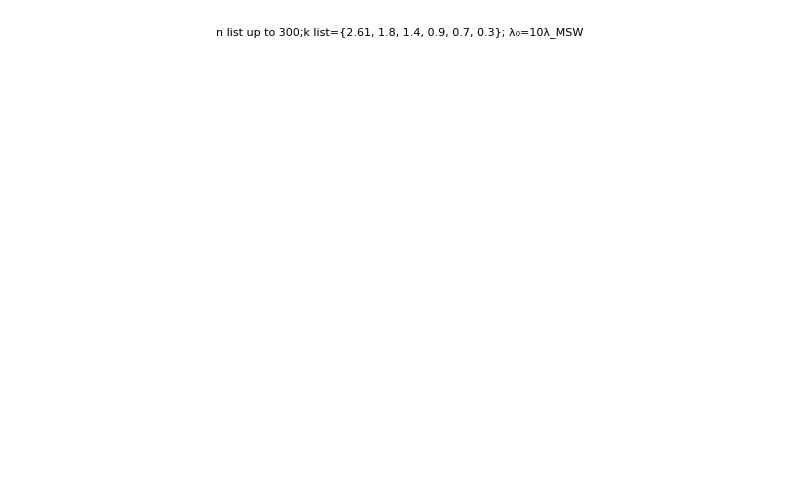

```mathematica
Show[
pltNList[nList1,kNListTest,aNListTest,phiNListTest,thetamV,endpointN/150,"n list up to 300;",Blue,freq6Ticks,"Distance (km)"],
pltNum[kNListTest,aNListTest,phiNListTest,thetamV,endpointN/150,"k list="<>ToString[Table[N[kNListTest[[n]],3],{n,1,Length@kNListTest}]]<>"; λ_0="<>ToString[fraction]<>"λ_MSW",{Red,Thickness[0.004],Dashing[{0.004,0.03}]},None,None]
]
```

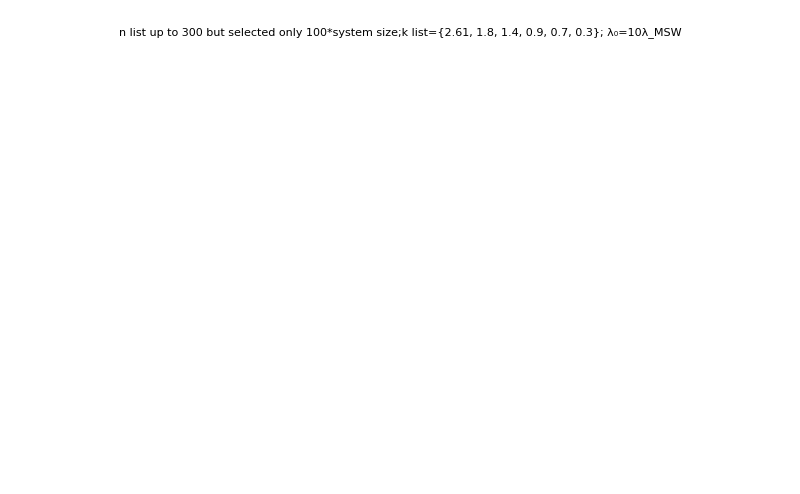

```mathematica
Show[
pltNList[nList2,kNListTest,aNListTest,phiNListTest,thetamV,endpointN/150,"n list up to 300 but selected only 100*system size;",Blue,freq6Ticks,"Distance (km)"],
pltNum[kNListTest,aNListTest,phiNListTest,thetamV,endpointN/150,"k list="<>ToString[Table[N[kNListTest[[n]],3],{n,1,Length@kNListTest}]]<>"; λ_0="<>ToString[fraction]<>"λ_MSW",{Red,Thickness[0.004],Dashing[{0.004,0.03}]},None,None]
]
```